# Spiral Repellor

## Flat Submanifold: Non-Compact

### y substitution (+)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x) in the flat case*)
de1:=x'=-3*Sqrt[(x+z)/3]*x*(1+wx+ϵ*x)-q*x*Sqrt[(x+z)/3]*z
de2:=z'=-3*Sqrt[(x+z)/3]*z + q*x*Sqrt[(x+z)/3]*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z→-x},{x→0,z→0},{x→-(1+wx)/ϵ,z→0},{x→0,z→0},{x→3/q,z→-3/q},{x→(3 (1+wx))/(q-3 ϵ),z→-(3 (1+wx))/(q-3 ϵ)},{x→3/q,z→-(3 (q+q wx+3 ϵ))/q^2}}

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z→-1. x},{x→3.,z→-3.},{x→0.,z→0.},{x→2.,z→0.},{x→3.,z→0.75}}

```mathematica
FP[1]={x,z/.FPs[[1,1]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
FP[4]={x/.FPs[[4,1]],z/.FPs[[4,2]]};
FP[5]={x/.FPs[[5,1]],z/.FPs[[5,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,z]}, {D[de2,x],D[de2,z]}}];
J//MatrixForm
```

((-1.29904 x+1.08253 x^2+(-0.866025-0.57735 z) z)/(√(x+z)) | (x (-0.433013-0.360844 x-0.866025 z))/(√(x+z))
(z (-3+3 x+2 z))/(2 √3 √(x+z)) | ((-3+x) (2 x+3 z))/(2 √3 √(x+z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,5}];
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√3) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
-1. x) | (ComplexInfinity | ComplexInfinity
ComplexInfinity | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]
(3.
-3.) | (ComplexInfinity | ComplexInfinity
Indeterminate | Indeterminate) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{Indeterminate,Indeterminate}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{Indeterminate,Indeterminate}}]
(0.
0.) | (Indeterminate | Indeterminate
Indeterminate | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]
(2.
0.) | (1.22474 | -1.63299
0. | -0.816497) | (1.22474
-0.816497) | (1. | 0.
0.624695 | 0.780869)
(3.
0.75) | (2.51558 | -3.3541
0.838525 | 0.) | (1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.894427+0. ⅈ | 0.33541-0.295804 ⅈ
0.894427+0. ⅈ | 0.33541+0.295804 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
PhaseSpacexz=StreamPlot[{de1,de2},{x,0,5},{z,0,3},FrameLabel->{"x","z"}];
```

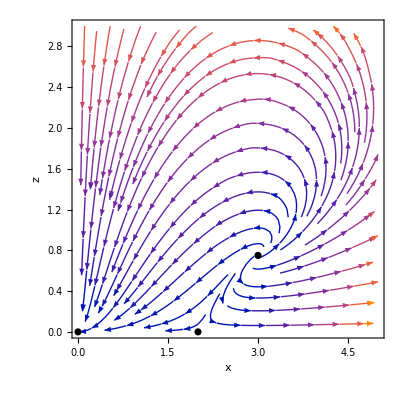

```mathematica
Show[PhaseSpacexz,FPShowxz]
```

### y substitution (-)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x) in the flat case*)
de1:=x'=-3*-Sqrt[(x+z)/3]*x*(1+wx+ϵ*x)-q*x*-Sqrt[(x+z)/3]*z
de2:=z'=-3*-Sqrt[(x+z)/3]*z + q*x*-Sqrt[(x+z)/3]*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z→-1. x},{x→3.,z→-3.},{x→0.,z→0.},{x→2.,z→0.},{x→3.,z→0.75}}

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{z→-1. x},{x→3.,z→-3.},{x→0.,z→0.},{x→2.,z→0.},{x→3.,z→0.75}}

```mathematica
FP[1]={x,z/.FPs[[1,1]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
FP[4]={x/.FPs[[4,1]],z/.FPs[[4,2]]};
FP[5]={x/.FPs[[5,1]],z/.FPs[[5,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,z]}, {D[de2,x],D[de2,z]}}];
J//MatrixForm
```

((1.29904 x-1.08253 x^2+(0.866025+0.57735 z) z)/(√(x+z)) | (x (0.433013+0.360844 x+0.866025 z))/(√(x+z))
-(z (-3+3 x+2 z))/(2 √3 √(x+z)) | -((-3+x) (2 x+3 z))/(2 √3 √(x+z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,5}];
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(√3) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

Eigenvectors::inf: Input matrix contains an infinite entry.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Eigenvectors::mindet: Input matrix contains an indeterminate entry.

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
-1. x) | (ComplexInfinity | ComplexInfinity
ComplexInfinity | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{ComplexInfinity,ComplexInfinity}}]
(3.
-3.) | (ComplexInfinity | ComplexInfinity
Indeterminate | Indeterminate) | Eigenvalues[{{ComplexInfinity,ComplexInfinity},{Indeterminate,Indeterminate}}] | Eigenvectors[{{ComplexInfinity,ComplexInfinity},{Indeterminate,Indeterminate}}]
(0.
0.) | (Indeterminate | Indeterminate
Indeterminate | Indeterminate) | Eigenvalues[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}] | Eigenvectors[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]
(2.
0.) | (-1.22474 | 1.63299
0. | 0.816497) | (-1.22474
0.816497) | (1. | 0.
0.624695 | 0.780869)
(3.
0.75) | (-2.51558 | 3.3541
-0.838525 | 0.) | (-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.894427+0. ⅈ | 0.33541+0.295804 ⅈ
0.894427+0. ⅈ | 0.33541-0.295804 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
PhaseSpacexz=StreamPlot[{de1,de2},{x,0,5},{z,0,3},FrameLabel->{"x","z"}];
```

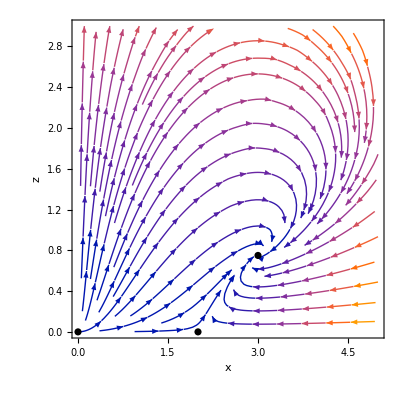

```mathematica
Show[PhaseSpacexz,FPShowxz]
```

### x(z, y)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=z'=-3*y*z + q*(3*y^2-z)*y*z
de2:=y'=-y^2-(1/6)*((3*y^2-z)+z+3*wx*(3*y^2-z)+3*ϵ*((3*y^2-z)^2))
```

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{z,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{z→0.75,y→-1.11803},{z→0.,y→-0.816497},{z→0.,y→0.},{z→2.,y→0.},{z→0.,y→0.816497},{z→0.75,y→1.11803}}

```mathematica
FP[1]={z/.FPs[[1,1]],y/.FPs[[1,2]]};
FP[2]={z/.FPs[[2,1]],y/.FPs[[2,2]]};
FP[3]={z/.FPs[[3,1]],y/.FPs[[3,2]]};
FP[4]={z/.FPs[[4,1]],y/.FPs[[4,2]]};
FP[5]={z/.FPs[[5,1]],y/.FPs[[5,2]]};
FP[6]={z/.FPs[[6,1]],y/.FPs[[6,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,z],D[de1,y]}, {D[de2,z],D[de2,y]}}];
J//MatrixForm
```

(y (-3+3 y^2-2 z) | (-3+9 y^2-z) z
-0.25-0.75 y^2+0.25 z | y (-1.5+4.5 y^2-1.5 z))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{z->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{z->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{z->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.75
-1.11803) | (0.838525 | 5.625
-1. | -3.3541) | (-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.921443+0. ⅈ | -0.343401+0.181711 ⅈ
0.921443+0. ⅈ | -0.343401-0.181711 ⅈ)
(0.
-0.816497) | (0.816497 | 0.
-0.75 | -1.22474) | (-1.22474
0.816497) | (0. | 1.
0.938647 | -0.344881)
(0.
0.) | (0. | 0.
-0.25 | 0.) | (0.
0.) | (0. | 1.
0. | 0.)
(2.
0.) | (0. | -10.
0.25 | 0.) | (0.+1.58114 ⅈ
0.-1.58114 ⅈ) | (-0.98773+0. ⅈ | 0.+0.156174 ⅈ
-0.98773+0. ⅈ | 0.-0.156174 ⅈ)
(0.
0.816497) | (-0.816497 | 0.
-0.75 | 1.22474) | (1.22474
-0.816497) | (0. | 1.
0.938647 | 0.344881)
(0.75
1.11803) | (-0.838525 | 5.625
-1. | 3.3541) | (1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.921443+0. ⅈ | 0.343401+0.181711 ⅈ
0.921443+0. ⅈ | 0.343401-0.181711 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowzy=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
PhaseSpacezy=StreamPlot[{de1,de2},{z,0,4},{y,-2,2},FrameLabel->{"z","y"}];
```

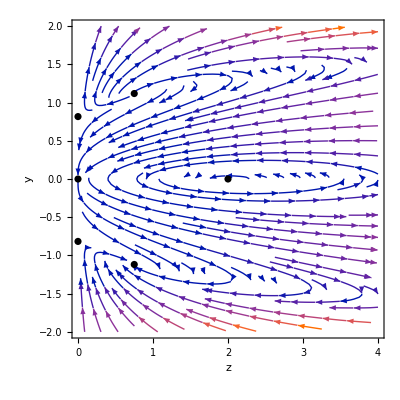

```mathematica
Show[PhaseSpacezy,FPShowzy]
```

### z(x, y)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*(3*y^2-x)
de2:=y'=-y^2-(1/6)*(x+(3*y^2-x)+3*wx*x+3*ϵ*x^2)
```

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-2.,y→0.},{x→0.,y→0.},{x→3.,y→-1.11803},{x→2.,y→-0.816497},{x→2.,y→0.816497},{x→3.,y→1.11803}}

```mathematica
FP[1]={x/.FPs[[1,1]],y/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y]}, {D[de2,x],D[de2,y]}}];
J//MatrixForm
```

(y (-1.5+3.5 x-3. y^2) | x (-1.5+1.75 x-9. y^2)
0.25+0.25 x | -3 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(-2.
0.) | (0. | 10.
-0.25 | 0.) | (0.+1.58114 ⅈ
0.-1.58114 ⅈ) | (0.98773+0. ⅈ | 0.+0.156174 ⅈ
0.98773+0. ⅈ | 0.-0.156174 ⅈ)
(0.
0.) | (0. | 0.
0.25 | 0.) | (0.
0.) | (0. | 1.
0. | 0.)
(3.
-1.11803) | (-5.86968 | -22.5
1. | 3.3541) | (-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.978492+0. ⅈ | -0.200564-0.0482403 ⅈ
0.978492+0. ⅈ | -0.200564+0.0482403 ⅈ)
(2.
-0.816497) | (-2.85774 | -8.
0.75 | 2.44949) | (-1.22474
0.816497) | (-0.979796 | 0.2
0.908739 | -0.417365)
(2.
0.816497) | (2.85774 | -8.
0.75 | -2.44949) | (1.22474
-0.816497) | (0.979796 | 0.2
0.908739 | 0.417365)
(3.
1.11803) | (5.86968 | -22.5
1. | -3.3541) | (1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.978492+0. ⅈ | 0.200564-0.0482403 ⅈ
0.978492+0. ⅈ | 0.200564+0.0482403 ⅈ)

```mathematica
(*Plot the fixed points*)
FPShowxy=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
PhaseSpacexy=StreamPlot[{de1,de2},{x,0,4},{y,-2,2},FrameLabel->{"x","y"}];
```

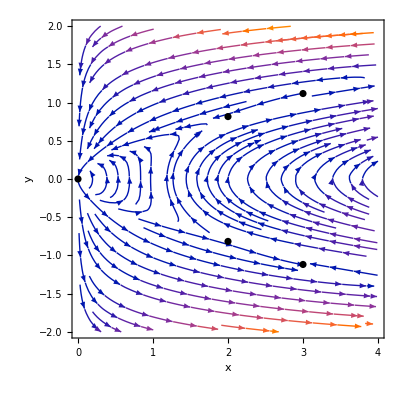

```mathematica
Show[PhaseSpacexy,FPShowxy]
```

## Full Case: Non-Compact Phase Spaces

### Non-Compact x - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→2.,z→0.},{x→3.,z→0.75},{x→0.,z→0.}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(2.
0.) | (1.5 | -2.
0. | -1.) | (1.5
-1.) | (1. | 0.
0.624695 | 0.780869)
(3.
0.75) | (2.25 | -3.
0.75 | 0.) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.894427+0. ⅈ | 0.33541-0.295804 ⅈ
0.894427+0. ⅈ | 0.33541+0.295804 ⅈ)
(0.
0.) | (-1.5 | 0.
0. | -3.) | (-3.
-1.5) | (0. | 1.
-1. | 0.)

```mathematica
(*Clear parameter values to find condition on wx to be a spiral repellor*)
Clear[q,ϵ,wx]
```

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{wx→-(2 q+3 ϵ)^2/(4 q^2)},{q→0,ϵ→0}}

```mathematica
wxCondition=wx/.wxCond[[1]]
```

-(2 q+3 ϵ)^2/(4 q^2)

```mathematica
(*Maximum value wx can be for the first fixed point to be complex for positive q and negative ϵ -> Fig. 9b*)
(*For this wx the two eigenvalues are the same*)
wxMax=wxCondition/.{ϵ->-0.25,q->1}
```

-0.390625

```mathematica
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Plot the fixed points*)
FPShowxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=dex;
DM[q_]=dez;
```

```mathematica
PhaseSpacexz=StreamPlot[{DE[wx,q,ϵ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}];
```

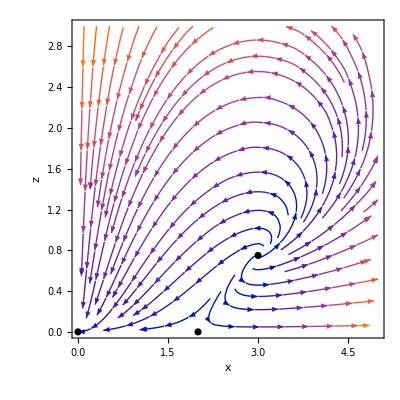

```mathematica
Show[PhaseSpacexz,FPShowxz]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11803,z→0.75},{x→3.,y→1.11803,z→0.75}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.25 x (2.+3. x)) | (0. | -0.75 x (2.-0.333333 x+1. x^2) | 0.
0.0833333+0.25 x | 0. | -1/6
0. | 0.75 (-3.+x) x (0.666667+1. x) | 0.) | (0
(0.-0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)
(0.+0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)) | (0.666667/(0.333333+1. x) | 0 | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | -((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | ((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -1/6
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(2.
-0.816497
0.) | (-1.22474 | 0. | 1.63299
0.583333 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.600469 | -0.275783 | 0.750587)
(2.
0.816497
0.) | (1.22474 | 0. | -1.63299
0.583333 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.600469 | 0.275783 | 0.750587)
(3.
-1.11803
0.75) | (-2.51558 | 0. | 3.3541
0.833333 | 2.23607 | -1/6
-0.838525 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ)
(3.
1.11803
0.75) | (2.51558 | 0. | -3.3541
0.833333 | -2.23607 | -1/6
0.838525 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ)

```mathematica
FPShowxyz=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Plot the Einstein fixed points*)
Einsteinxyz=ParametricPlot3D[{x,0,0.25 x (2.+3. x)},{x,0,15},{z,0,10},PlotStyle->{{Thickness[.1]}}];
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(x+z);
FFS=Sqrt[ffs];
```

```mathematica
FFSPlus=ParametricPlot3D[{x,FFS,z},{x,0,15},{z,0,10},PlotStyle->Darker[Green]];
FFSMinus=ParametricPlot3D[{x,-FFS,z},{x,0,15},{z,0,10},PlotStyle->Darker[Green]];
```

```mathematica
Eq1[q_,wx_,ϵ_]=de1;
Eq2[wx_,ϵ_]=de2;
Eq3[q_]=de3;
```

```mathematica
PhaseSpacexyz=StreamPlot3D[{Eq1[q,wx,ϵ],Eq2[wx,ϵ],Eq3[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"},StreamMarkers->"Arrow"];
```

```mathematica
Show[PhaseSpacexyz,FPShowxyz,Einsteinxyz,FFSPlus,FFSMinus]
```

-Graphics3D-

## Non-Compact Numeric Phase Spaces

### x - y - z

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11803,z→0.75},{x→3.,y→1.11803,z→0.75}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.25 x (2.+3. x)) | (0. | -0.75 x (2.-0.333333 x+1. x^2) | 0.
0.0833333+0.25 x | 0. | -1/6
0. | 0.75 (-3.+x) x (0.666667+1. x) | 0.) | (0
(0.-0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)
(0.+0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)) | (0.666667/(0.333333+1. x) | 0 | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | -((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | ((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -1/6
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(2.
-0.816497
0.) | (-1.22474 | 0. | 1.63299
0.583333 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.600469 | -0.275783 | 0.750587)
(2.
0.816497
0.) | (1.22474 | 0. | -1.63299
0.583333 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.600469 | 0.275783 | 0.750587)
(3.
-1.11803
0.75) | (-2.51558 | 0. | 3.3541
0.833333 | 2.23607 | -1/6
-0.838525 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ)
(3.
1.11803
0.75) | (2.51558 | 0. | -3.3541
0.833333 | -2.23607 | -1/6
0.838525 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Analyse the unstable spiral fixed point*)
(*z and y values at the spiral point for this case*)
zSpiral=-(3 (q+q wx+3 ϵ))/q^2
ySpiralPlus=(√(-q wx-3 ϵ))/q
ySpiralMinus=-(√(-q wx-3 ϵ))/q
```

0.75

1.11803

-1.11803

```mathematica
traj[x0_,y0_,z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,y1[0]==y0,z1[0]==z0}, {x1,y1,z1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
flatx0=3;
flatz0=1;
flaty0=Sqrt[(flatx0+flatz0)/3]
```

2/(√3)

```mathematica
(*Flat trajectories*)
sol[1]=traj[flatx0,flaty0,flatz0];  
sol[2]=traj[flatx0,-flaty0,flatz0];
```

NDSolve::ndsz: At t == -10.074, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 10.074, step size is effectively zero; singularity or stiff system suspected.

```mathematica
(*Open trajectories*)
sol[3]=traj[Sqrt[(0.1+0.009)/3]+0.2,0.1,0.009];
```

```mathematica
(*Closed trajectories*)
sol[4]=traj[5,0.1,1];
sol[5]=traj[10,0.1,1];
```

```mathematica
FPShowNumericxyz=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*3D Numeric Plot*)NumericxyzFlat=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.sol[1], {t,-50,50},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"x","y","z"}];
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NumericxyzFlat2=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.sol[2], {t,-50,50},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"x","y","z"}];
```

```mathematica
NumericxyzOpen=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.sol[3], {t,-50,50},PlotStyle -> {{Pink, Opacity[0.75]}}],AxesLabel->{"x","y","z"}];
```

```mathematica
NumericxyzClosed=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.sol[4], {t,-50,50},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"x","y","z"}];
```

```mathematica
NumericxyzClosed2=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.sol[5], {t,-50,50},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"x","y","z"}];
```

```mathematica
Show[FPShowNumericxyz,NumericxyzFlat,NumericxyzFlat2,NumericxyzOpen,NumericxyzClosed,NumericxyzClosed2,PlotRange->{{0,10},{-5,5},{0,8}}]
```

-Graphics3D-

```mathematica
FPShowNumericxy=ListPlot[{{0,0},{2,-0.816496580927726},{2,0.816496580927726},{3,-1.118033988749895},{3,1.118033988749895}},PlotStyle->Black];
```

```mathematica
(*2D Numeric Plot*)
Numericxy=ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,5}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{-3,3}}],AxesLabel->{"x","y"}];
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

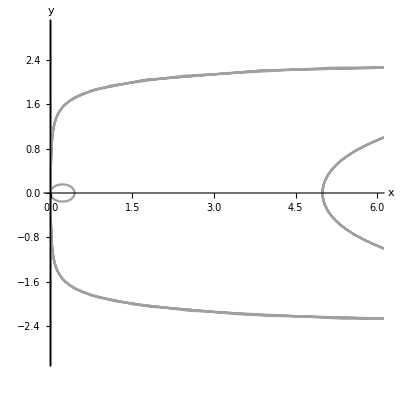

```mathematica
Show[Numericxy]
```

### a - y Phase Space

```mathematica
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z+ q*x*y*z
de4:=a'=a*y
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,y,z,a}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.,a→0.},{x→2.,y→-0.816497,z→0.,a→0.},{x→2.,y→0.816497,z→0.,a→0.},{x→3.,y→-1.11803,z→0.75,a→0.},{x→3.,y→1.11803,z→0.75,a→0.}}

```mathematica
FP[1]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]],a/.FPs[[2,4]]};
FP[2]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]],a/.FPs[[3,4]]};
FP[3]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]],a/.FPs[[4,4]]};
FP[4]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]],a/.FPs[[5,4]]};
FP[5]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]],a/.FPs[[6,4]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z],D[de1,a]},{D[de2,x],D[de2,y],D[de2,z],D[de2,a]},{D[de3,x],D[de3,y],D[de3,z],D[de3,a]},{D[de4,x],D[de4,y],D[de4,z],D[de4,a]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y | 0
0.0833333+0.25 x | -2 y | -1/6 | 0
y z | (-3+x) z | (-3+x) y | 0
0 | a | 0 | y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]],a->FPs[[i,4]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]],a->FPs[[i,4]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]],a->FPs[[i,4]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.
0.
0.
0.) | (0. | 0. | 0. | 0
0.0833333 | 0. | -1/6 | 0
0. | 0. | 0. | 0
0 | 0. | 0 | 0.) | (0.
0.
0.
0.) | (0. | 1. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 1.)
(2.
-0.816497
0.
0.) | (-1.22474 | 0. | 1.63299 | 0
0.583333 | 1.63299 | -1/6 | 0
0. | 0. | 0.816497 | 0
0 | 0. | 0 | -0.816497) | (1.63299
-1.22474
-0.816497
0.816497) | (0. | 1. | 0. | 0.
0.979796 | -0.2 | 0. | 0.
0. | 0. | 0. | 1.
0.600469 | -0.275783 | 0.750587 | 0.)
(2.
0.816497
0.
0.) | (1.22474 | 0. | -1.63299 | 0
0.583333 | -1.63299 | -1/6 | 0
0. | 0. | -0.816497 | 0
0 | 0. | 0 | 0.816497) | (-1.63299
1.22474
-0.816497
0.816497) | (0. | 1. | 0. | 0.
0.979796 | 0.2 | 0. | 0.
0.600469 | 0.275783 | 0.750587 | 0.
0. | 0. | 0. | 1.)
(3.
-1.11803
0.75
0.) | (-2.51558 | 0. | 3.3541 | 0
0.833333 | 2.23607 | -1/6 | 0
-0.838525 | 0. | 0. | 0
0 | 0. | 0 | -1.11803) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ
-1.11803+0. ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)
(3.
1.11803
0.75
0.) | (2.51558 | 0. | -3.3541 | 0
0.833333 | -2.23607 | -1/6 | 0
0.838525 | 0. | 0. | 0
0 | 0. | 0 | 1.11803) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ
1.11803+0. ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)

```mathematica
(*dexa:=x1'[a]==-3*(x1[a])*(1+wx+ϵ*x1[a])-q*x1[a]*z1[a]
deza:=z1'[a]==-3*z1[a]+ q*x1[a]*z1[a]
```

```mathematica
(*q=1;
wx=-0.5;
ϵ=-0.25;*)
```

```mathematica
(*traj[x0_,z0_]=NDSolve[{dexa,deza, x1[0]==x0,z1[0]==z0}, {x1,z1},{a,0,20}]; *)
```

```mathematica
(*sol[1]=traj[2,4];
sol[2]=traj[0.5,1];
sol[3]=traj[5,1];
sol[4]=traj[4,1];
sol[5]=traj[1,3];
sol[6]=traj[3,1];
sol[7]=traj[4,2];
sol[8]=traj[0,0];*)
```

```mathematica
(*ParametricPlot[Evaluate[Table[{x1[a],z1[a]}/.sol[i],{i,1,8}], {a,0,20},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{0,6}}],AxesLabel->{"x","z"}]*)
```

```mathematica
(*xzsol=NDSolve[{dexa,deza,x1[0]==0.5,z1[0]==0.009},{x1,z1},{a,0,20}]*)
```

```mathematica
(*x2=x1/.xzsol[[1,1]];*)
```

```mathematica
(*z2=z1/.xzsol[[1,2]];*)
```

```mathematica
(*dey:=y1'[t]==-y1[t]^2-(1/6)*(x2[t]+z2[t]+3*wx*x2[t]+3*ϵ*x2[t]^2)
dea:=a1'[t]==a1[t]*y1[t]*)
```

```mathematica
(*aysol=NDSolve[{dey,dea, a1[0]==1,y1[0]==0.1}, {a1,y1},{t,-20,20}];*)
```

```mathematica
(*ParametricPlot[Evaluate[{a1[t],y1[t]}/.aysol], {t,-20,20},PlotRange->{{0,1.5},{-1,1}},PlotStyle -> {{Gray, Opacity[0.75]}},AxesLabel->{"a","y"}]*)
```

### a, x, z and y as functions of t

```mathematica
(*de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
de4t:=a1'[t]==a1[t]*y1[t];*)
```

```mathematica
(*q=1;
wx=-0.5;
ϵ=-0.25;*)
```

```mathematica
(*traj[x0_,y0_,z0_,a0_]=NDSolve[{de1t,de2t,de3t,de4t, x1[0]==x0,y1[0]==y0,z1[0]==z0,a1[0]==a0}, {x1,y1,z1,a1},{t,-50,50}]; *)
```

```mathematica
(*sol[1]=traj[3,-1,0.009,1];
sol[2]=traj[0.5,0.1,0.009,1];
sol[3]=traj[5,0.1,0.009,1];
sol[4]=traj[4,0.1,0.009,1];
sol[5]=traj[1,0.1,0.009,1];
sol[6]=traj[3,2,0.009,1];
sol[7]=traj[4,3,0.009,1];
sol[8]=traj[1,2.5,0.009,1];*)
```

```mathematica
(*FPShoway=ListPlot[{{0,0},{0,0.816496580927726},{0,-0.816496580927726},{0,1.118033988749895},{0,-1.118033988749895}},PlotStyle->Black];*)
```

```mathematica
(*Numericay=ParametricPlot[Evaluate[Table[{a1[t],y1[t]}/.sol[i],{i,1,8}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{-3,3}}],AxesLabel->{"a","y"}];*)
```

```mathematica
(*Show[Numericay,FPShoway]*)
```

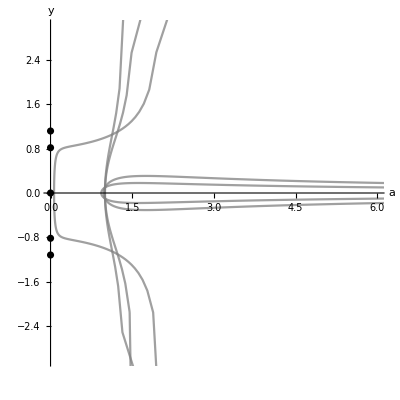

### Non-Compact Ωx-Ωm Density Parameter Phase Space

#### Flat Case

```mathematica
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+(1-Ωx)*(1-q/Ωs))
deΩs:=Ωs'=Ωs*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+(1-Ωx))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deΩs==0},{Ωx,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx→0.8,Ωs→0.266667},{Ωx→1.,Ωs→0.5}}

```mathematica
FP[1]={Ωx/.FPs[[1,1]],Ωs/.FPs[[1,2]]};
FP[2]={Ωx/.FPs[[2,1]],Ωs/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deΩx,Ωx],D[deΩx,Ωs]},{D[deΩs,Ωx],D[deΩs,Ωs]}}];
J//MatrixForm
```

((-1.+Ωs (1.5-3. Ωx)+3.5 Ωx-2.25 Ωx^2)/Ωs | (0.75 Ωx (1.33333-2.33333 Ωx+1. Ωx^2))/Ωs^2
-1.5 Ωs-1.5 Ωx | 3.-1.5 Ωx)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{Ωx->FPs[[i,1]],Ωs->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{Ωx->FPs[[i,1]],Ωs->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{Ωx->FPs[[i,1]],Ωs->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.8
0.266667) | (0.45 | 0.9
-1.6 | 1.8) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.3375-0.496078 ⅈ | 0.8+0. ⅈ
0.3375+0.496078 ⅈ | 0.8+0. ⅈ)
(1.
0.5) | (-1. | -6.66134×10^-16
-2.25 | 1.5) | (1.5
-1.) | (2.77726×10^-16 | -1.
-0.743294 | -0.668965)

```mathematica
FPShowFlatΩxΩs=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
DS[wx_,q_,ϵ_]=deΩs;
```

```mathematica
PhaseSpaceFlatΩxΩs=StreamPlot[{DE[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1.5},{Ωs,0,3},FrameLabel->{"Ωx","Ωs"}];
```

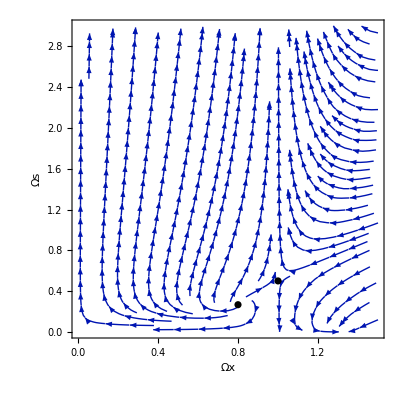

```mathematica
Show[PhaseSpaceFlatΩxΩs,FPShowFlatΩxΩs]
```

#### Full Case

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+Ωm*(1-q/Ωs))
deΩm:=Ωm'=Ωm*(-1+Ωm+Ωx*((q/Ωs)+1+3*wx+3*ϵ*Ωx/Ωs))
deΩs:=Ωs'=Ωs*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+Ωm)
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deΩm==0,deΩs==0},{Ωx,Ωm,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx→0.8,Ωm→0.2,Ωs→0.266667},{Ωx→1.,Ωm→0.,Ωs→0.5}}

```mathematica
FP[1]={Ωx/.FPs[[1,1]],Ωm/.FPs[[1,2]],Ωs/.FPs[[1,3]]};
FP[2]={Ωx/.FPs[[2,1]],Ωm/.FPs[[2,2]],Ωs/.FPs[[2,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deΩx,Ωx],D[deΩx,Ωm],D[deΩx,Ωs]},{D[deΩm,Ωx],D[deΩm,Ωm],D[deΩm,Ωs]},{D[deΩs,Ωx],D[deΩs,Ωm],D[deΩs,Ωs]}}];
J//MatrixForm
```

((Ωm (-1.+Ωs)+Ωs (0.5-1. Ωx)+(1.5-2.25 Ωx) Ωx)/Ωs | ((-1+Ωs) Ωx)/Ωs | (Ωx (1. Ωm+(-0.75+0.75 Ωx) Ωx))/Ωs^2
Ωm (-0.5+(1-1.5 Ωx)/Ωs) | -1+2 Ωm+(-0.5+(1-0.75 Ωx)/Ωs) Ωx | (0.75 Ωm Ωx (-1.33333+1. Ωx))/Ωs^2
-0.5 Ωs-1.5 Ωx | Ωs | 2.+Ωm-0.5 Ωx)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{Ωx->FPs[[i,1]],Ωm->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{Ωx->FPs[[i,1]],Ωm->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{Ωx->FPs[[i,1]],Ωm->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.8
0.2
0.266667) | (-1.75 | -2.2 | 0.9
-0.25 | 0.2 | -0.9
-1.33333 | 0.266667 | 1.8) | (-2.+0. ⅈ
1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (-0.923077+0. ⅈ | -0.230769+0. ⅈ | -0.307692+0. ⅈ
0.289404-0.425384 ⅈ | -0.289404+0.425384 ⅈ | 0.685994+0. ⅈ
0.289404+0.425384 ⅈ | -0.289404-0.425384 ⅈ | 0.685994+0. ⅈ)
(1.
0.
0.5) | (-2. | -1. | 0.
0. | -1. | 0.
-1.75 | 0.5 | 1.5) | (-2.
1.5
-1.) | (0.894427 | 0. | 0.447214
0. | 0. | 1.
-0.59655 | 0.59655 | -0.536895)

```mathematica
FPShowΩxΩmΩs=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
DM[wx_,q_,ϵ_]=deΩm;
DS[wx_,q_,ϵ_]=deΩs;
```

```mathematica
PhaseSpaceΩxΩmΩs=StreamPlot3D[{DE[wx,q,ϵ],DM[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1},{Ωm,0,1},{Ωs,0,1},AxesLabel->{"Ωx","Ωm","Ωs"},StreamMarkers->"Arrow"];
```

```mathematica
Show[PhaseSpaceΩxΩmΩs,FPShowΩxΩmΩs]
```

-Graphics3D-

```mathematica
deΩxt:=Ωx1'[t]==Ωx1[t]*(-(1+3*wx)+Ωx1[t]*(-3*(ϵ/Ωs1[t])+1+3*wx+3*ϵ*(Ωx1[t]/Ωs1[t]))+Ωm1[t]*(1-q/Ωs1[t]))
deΩmt:=Ωm1'[t]==Ωm1[t]*(-1+Ωm1[t]+Ωx1[t]*((q/Ωs1[t])+1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t]))
deΩst:=Ωs1'[t]==Ωs1[t]*(2+Ωx1[t]*(1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t])+Ωm1[t])
```

```mathematica
traj[x0_,z0_,s0_]=NDSolve[{deΩxt,deΩmt,deΩst,Ωx1[0]==x0,Ωm1[0]==z0,Ωs1[0]==s0}, {Ωx1,Ωm1,Ωs1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition z0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6889,0.3111,1];
```

NDSolve::ndsz: At t == -18.6632, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[2]=traj[0.5,0.5,1];
```

NDSolve::ndsz: At t == -18.7265, step size is effectively zero; singularity or stiff system suspected.

```mathematica
PhaseSpaceΩxΩmΩs2=ParametricPlot3D[Evaluate[Table[{Ωx1[t],Ωm1[t],Ωs1[t]}/.sol[i],{i,1,2}], {t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"Ωx","Ωm","Ωs"}];
```

InterpolatingFunction::dmval: Input value {-99.9959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[PhaseSpaceΩxΩmΩs,PhaseSpaceΩxΩmΩs2,FPShowΩxΩmΩs]
```

-Graphics3D-

### Non-Compact Ωx-H-Ωm Density Parameter Phase Space

#### Flat Case

```mathematica
deΩx:=Ωx'=Ωx*H*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+(1-Ωx)*(1-q/Ωs))
deH:=H'=-H^2-(H^2/2)*(Ωx*(1+3*wx)+(1-Ωx)+3*ϵ*Ωx^2/Ωs)
deΩs:=Ωs'=Ωs*H*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+(1-Ωx))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deH==0,deΩs==0},{Ωx,H,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H→0.},{Ωx→0.8,Ωs→0.266667},{Ωx→1.,Ωs→0.5}}

```mathematica
FP[1]={Ωx,H/.FPs[[1,1]],Ωs};
FP[2]={Ωx/.FPs[[2,1]],H,Ωs/.FPs[[2,2]]};
FP[3]={Ωx/.FPs[[3,1]],H,Ωs/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deΩx,Ωx],D[deΩx,H],D[deΩx,Ωs]},{D[deH,Ωx],D[deH,H],D[deH,Ωs]},{D[deΩs,Ωx],D[deΩs,H],D[deΩs,Ωs]}}];
J//MatrixForm
```

((H (-1.+Ωs (1.5-3. Ωx)+3.5 Ωx-2.25 Ωx^2))/Ωs | -(1.5 Ωx (0.666667-1.16667 Ωx+0.5 Ωx^2+Ωs (-1.+1. Ωx)))/Ωs | (0.75 H Ωx (1.33333-2.33333 Ωx+1. Ωx^2))/Ωs^2
(H^2 (0.75 Ωs+0.75 Ωx))/Ωs | H (-3.+1.5 Ωx+(0.75 Ωx^2)/Ωs) | -(0.375 H^2 Ωx^2)/Ωs^2
H (-1.5 Ωs-1.5 Ωx) | Ωs (3.-1.5 Ωx)-0.75 Ωx^2 | H (3.-1.5 Ωx))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωs->FPs[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(Ωx
0.
Ωs) | (0. | -(1.5 Ωx (0.666667-1.16667 Ωx+0.5 Ωx^2+Ωs (-1.+1. Ωx)))/Ωs | 0.
0. | 0. | 0.
0. | Ωs (3.-1.5 Ωx)-0.75 Ωx^2 | 0.) | (0.
0.
0.) | (0. | 0. | 1.
1. | 0. | 0.
0. | 0. | 0.)
(0.8
H
0.266667) | (0.45 H | 4.996×10^-16 | 0.9 H
3. H^2 | 4.44089×10^-16 H | -3.375 H^2
-1.6 H | -1.66533×10^-16 | 1.8 H) | (Root[-2.96638×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1]
Root[-2.96638×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2]
Root[-2.96638×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3]) | (-(1. (2.3731×10^-16 H^2-1.8 H Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1]+1. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1]^2))/(H (-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1])) | -(1. H (0.+3. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1]))/(-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,1]) | 1.
-(1. (2.3731×10^-16 H^2-1.8 H Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2]+1. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2]^2))/(H (-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2])) | -(1. H (0.+3. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2]))/(-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,2]) | 1.
-(1. (2.3731×10^-16 H^2-1.8 H Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3]+1. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3]^2))/(H (-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3])) | -(1. H (0.+3. Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3]))/(-2.10942×10^-16 H+1.6 Root[-2.9663771439203×10^-16 H^3+2.25 H^2 #1-2.25 H #1^2+#1^3&,3]) | 1.)

```mathematica
HFixedPoints=ParametricPlot3D[{Ωx,0,Ωs},{Ωx,0,1},{Ωs,0,1}];
```

```mathematica
ΩFixedPoints1=ParametricPlot3D[{0.8,H,0.26666666666666666},{H,-1.5,1.5},PlotStyle->Black];
```

```mathematica
ΩFixedPoints2=ParametricPlot3D[{1.,H,0.5},{H,-1.5,1.5},PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
HEqn[wx_,q_,ϵ_]=deH;
DS[wx_,q_,ϵ_]=deΩs;
```

```mathematica
PhaseSpaceΩxHΩm=StreamPlot3D[{DE[wx,q,ϵ],HEqn[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1.5},{H,-1.5,1.5},{Ωs,0,1.5},AxesLabel->{"Ωx","H","Ωs"},StreamMarkers->"Arrow"];
```

```mathematica
Show[PhaseSpaceΩxHΩm,HFixedPoints,ΩFixedPoints1,ΩFixedPoints2,PlotRange->{{0,1},{-1.5,1.5},{0,1}}]
```

-Graphics3D-

#### Full Case

```mathematica
deΩx:=Ωx'=Ωx*H*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+Ωm*(1-q/Ωs))
deH:=H'=-H^2-(H^2/2)*(Ωx*(1+3*wx)+Ωm+3*ϵ*Ωx^2/Ωs)
deΩm:=Ωm'=Ωm*H*(-1+Ωm+Ωx*((q/Ωs)+1+3*wx+3*ϵ*Ωx/Ωs))
deΩs:=Ωs'=Ωs*H*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+Ωm)
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deH==0,deΩm==0,deΩs==0},{Ωx,H,Ωm,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H→0.},{Ωx→0.8,Ωm→0.2,Ωs→0.266667},{Ωx→1.,Ωm→0.,Ωs→0.5}}

```mathematica
FP[1]={Ωx,H/.FPs[[1,1]],Ωm,Ωs};
FP[2]={Ωx/.FPs[[2,1]],H,Ωm/.FPs[[2,2]],Ωs/.FPs[[2,3]]};
FP[3]={Ωx/.FPs[[3,1]],H,Ωm/.FPs[[3,2]],Ωs/.FPs[[3,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deΩx,Ωx],D[deΩx,H],D[deΩx,Ωm],D[deΩx,Ωs]},{D[deH,Ωx],D[deH,H],D[deH,Ωm],D[deH,Ωs]},{D[deΩm,Ωx],D[deΩm,H],D[deΩm,Ωm],D[deΩm,Ωs]},{D[deΩs,Ωx],D[deΩs,H],D[deΩs,Ωm],D[deΩs,Ωs]}}];
J//MatrixForm
```

((H (Ωm (-1.+1. Ωs)+Ωs (0.5-1. Ωx)+(1.5-2.25 Ωx) Ωx))/Ωs | (Ωx (Ωm (-1.+Ωs)+Ωs (0.5-0.5 Ωx)+(0.75-0.75 Ωx) Ωx))/Ωs | (H (-1+Ωs) Ωx)/Ωs | (0.75 H Ωx (1.33333 Ωm+Ωx (-1.+1. Ωx)))/Ωs^2
(H^2 (0.25 Ωs+0.75 Ωx))/Ωs | H (-2-Ωm+0.5 Ωx+(0.75 Ωx^2)/Ωs) | -H^2/2 | -(0.375 H^2 Ωx^2)/Ωs^2
H Ωm (-0.5+(1-1.5 Ωx)/Ωs) | Ωm (-1+Ωm+(-0.5+(1-0.75 Ωx)/Ωs) Ωx) | H (-1+2 Ωm+(-0.5+(1-0.75 Ωx)/Ωs) Ωx) | (0.75 H Ωm Ωx (-1.33333+1. Ωx))/Ωs^2
H (-0.5 Ωs-1.5 Ωx) | Ωs (2+Ωm+Ωx (-0.5-(0.75 Ωx)/Ωs)) | H Ωs | H (2.+1. Ωm-0.5 Ωx))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωm->FPs[[i,3]],Ωs->FPs[[i,4]]}]//MatrixForm,Eigenvalues[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωm->FPs[[i,3]],Ωs->FPs[[i,4]]}]//MatrixForm,Eigenvectors[J/.{Ωx->FPs[[i,1]],H->FPs[[i,2]],Ωm->FPs[[i,3]],Ωs->FPs[[i,4]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(Ωx
0.
Ωm
Ωs) | (0. | (Ωx (Ωm (-1.+Ωs)+Ωs (0.5-0.5 Ωx)+(0.75-0.75 Ωx) Ωx))/Ωs | 0. | 0.
0. | 0. | 0. | 0.
0. | Ωm (-1+Ωm+(-0.5+(1-0.75 Ωx)/Ωs) Ωx) | 0. | 0.
0. | Ωs (2+Ωm+Ωx (-0.5-(0.75 Ωx)/Ωs)) | 0. | 0.) | (0.
0.
0.
0.) | (0. | 0. | 0. | 1.
0. | 0. | 1. | 0.
1. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0.8
H
0.2
0.266667) | (-1.75 H | -2.91434×10^-16 | -2.2 H | 0.9 H
2.5 H^2 | 0. | -H^2/2 | -3.375 H^2
-0.25 H | -6.66134×10^-17 | 0.2 H | -0.9 H
-1.33333 H | 0. | 0.266667 H | 1.8 H) | (0
Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]
Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]
Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]) | (1.59649 | -1.58021×10^16 H | 1.23246 | 1.
-(0.8 (1. H^2 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]-3.33333 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]^2+1.66667 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]^3))/(H (0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]^2)) | -1.875 H | -(1. (0.+2.2 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]-0.333333 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]^2))/(0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,1]^2) | 1.
-(0.8 (1. H^2 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]-3.33333 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]^2+1.66667 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]^3))/(H (0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]^2)) | -1.875 H | -(1. (0.+2.2 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]-0.333333 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]^2))/(0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,2]^2) | 1.
-(0.8 (1. H^2 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]-3.33333 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]^2+1.66667 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]^3))/(H (0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]^2)) | -1.875 H | -(1. (0.+2.2 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]-0.333333 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]^2))/(0.-0.266667 H Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]+1.77778 Root[4.5 H^3-2.25 H^2 #1-0.25 H #1^2+#1^3&,3]^2) | 1.)
(1.
H
0.
0.5) | (-2. H | 0. | -1. H | 0.
1.75 H^2 | 0. | -H^2/2 | -1.5 H^2
0. | 0. | -1. H | 0.
-1.75 H | 0. | 0.5 H | 1.5 H) | (-2. H
1.5 H
-1. H
0.) | (2. | -1. H | 0 | 1.
0 | -1. H | 0 | 1.
1.11111 | -1. H | -1.11111 | 1.
0 | 1. | 0 | 0)

```mathematica
deΩxt:=Ωx1'[t]==Ωx1[t]*H1[t]*(-(1+3*wx)+Ωx1[t]*(-3*(ϵ/Ωs1[t])+1+3*wx+3*ϵ*(Ωx1[t]/Ωs1[t]))+Ωm1[t]*(1-q/Ωs1[t]))
deHt:=H1'[t]==-H1[t]^2-(H1[t]^2/2)*(Ωx1[t]*(1+3*wx)+Ωm1[t]+3*ϵ*Ωx1[t]^2/Ωs1[t])
deΩmt:=Ωm1'[t]==Ωm1[t]*H1[t]*(-1+Ωm1[t]+Ωx1[t]*((q/Ωs1[t])+1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t]))
deΩst:=Ωs1'[t]==Ωs1[t]*H1[t]*(2+Ωx1[t]*(1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t])+Ωm1[t])
```

```mathematica
traj[x0_,H0_,z0_,s0_]=NDSolve[{deΩxt,deHt,deΩmt,deΩst, Ωx1[0]==x0,H1[0]==H0,Ωm1[0]==z0,Ωs1[0]==s0}, {Ωx1,H1,Ωm1,Ωs1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition H0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6889,0.5,0.3111,1];
sol[2]=traj[0.6889,0.7,0.3111,1];
sol[3]=traj[0.6889,1,0.3111,1];
sol[4]=traj[0.6889,-0.5,0.3111,1];
sol[5]=traj[0.6889,-0.7,0.3111,1];
sol[6]=traj[0.6889,-1,0.3111,1];
sol[7]=traj[0.6889,0.3,0.3111,1];
sol[8]=traj[0.6889,0.1,0.3111,1];
sol[9]=traj[0.6889,-0.3,0.3111,1];
sol[10]=traj[0.6889,-0.1,0.3111,1];
sol[11]=traj[0.6889,-0.6,0.3111,1];
sol[12]=traj[0.6889,0.6,0.3111,1];
```

NDSolve::ndsz: At t == -20.5502, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -14.3263, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -10.213, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 20.5502, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 14.3263, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 10.213, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -33.7925, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 33.7925, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 16.8437, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -16.8437, step size is effectively zero; singularity or stiff system suspected.

```mathematica
HFixedPoints=ParametricPlot3D[{Ωx,0,Ωm},{Ωx,0,1},{Ωm,0,1}];
```

```mathematica
ΩFixedPoints1=ParametricPlot3D[{0.8,H,0.2},{H,-1.5,1.5}];
```

```mathematica
ΩFixedPoints2=ParametricPlot3D[{1.,H,0},{H,-1.5,1.5}];
```

```mathematica
PhaseSpaceΩxHΩm=ParametricPlot3D[Evaluate[Table[{Ωx1[t],H1[t],Ωm1[t]}/.sol[i],{i,1,12}], {t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"Ωx","H","Ωm"},PlotRange->{{0,1},{-1.2,1.2},{0,1}}];
```

InterpolatingFunction::dmval: Input value {-99.9959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[PhaseSpaceΩxHΩm,HFixedPoints,ΩFixedPoints1,ΩFixedPoints2]
```

-Graphics3D-

### Non-Compact Ωx-y-Ωm Density Parameter Phase Space

```mathematica
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(1+3*wx-9*y^2*ϵ+9*ϵ*Ωx*y^2)+Ωm*(1-3*q*y^2))
dey:=y'=-y^2-(y^2/2)*(Ωm+Ωx*(1+3*wx)+9*ϵ*y^2*Ωx^2)
deΩm:=Ωm'=Ωm*(-1+Ωm+Ωx*(3*q*y^2+1+3*wx+9*ϵ*Ωx*y^2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,dey==0,deΩm==0},{Ωx,y,Ωm}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx→0.8,y→-1.11803,Ωm→0.2},{Ωx→1.,y→-0.816497,Ωm→0.},{Ωx→0.,y→0.,Ωm→1.},{Ωx→1.,y→0.,Ωm→0.},{Ωx→1.,y→0.816497,Ωm→0.},{Ωx→0.8,y→1.11803,Ωm→0.2},{Ωx→0.,y→0.,Ωm→0.}}

```mathematica
FP[1]={Ωx/.FPs[[1,1]],y/.FPs[[1,2]],Ωm/.FPs[[1,3]]};
FP[2]={Ωx/.FPs[[2,1]],y/.FPs[[2,2]],Ωm/.FPs[[2,3]]};
FP[3]={Ωx/.FPs[[3,1]],y/.FPs[[3,2]],Ωm/.FPs[[3,3]]};
FP[4]={Ωx/.FPs[[4,1]],y/.FPs[[4,2]],Ωm/.FPs[[4,3]]};
FP[5]={Ωx/.FPs[[5,1]],y/.FPs[[5,2]],Ωm/.FPs[[5,3]]};
FP[6]={Ωx/.FPs[[6,1]],y/.FPs[[6,2]],Ωm/.FPs[[6,3]]};
FP[7]={Ωx/.FPs[[7,1]],y/.FPs[[7,2]],Ωm/.FPs[[7,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deΩx,Ωx],D[deΩx,y],D[deΩx,Ωm]},{D[dey,Ωx],D[dey,y],D[dey,Ωm]},{D[deΩm,Ωx],D[deΩm,y],D[deΩm,Ωm]}}];
J//MatrixForm
```

(0.5+(1.-3. y^2) Ωm+(-1.+4.5 y^2) Ωx-6.75 y^2 Ωx^2 | Ωx (-6 y Ωm+y (4.5-4.5 Ωx) Ωx) | Ωx-3 y^2 Ωx
0.25 y^2+2.25 y^4 Ωx | y (-2.-1. Ωm+0.5 Ωx+4.5 y^2 Ωx^2) | -y^2/2
Ωm (-0.5+y^2 (3-4.5 Ωx)) | y Ωm (6-4.5 Ωx) Ωx | -1+2 Ωm+(-0.5+y^2 (3-2.25 Ωx)) Ωx)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{Ωx->FPs[[i,1]],y->FPs[[i,2]],Ωm->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{Ωx->FPs[[i,1]],y->FPs[[i,2]],Ωm->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{Ωx->FPs[[i,1]],y->FPs[[i,2]],Ωm->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.8
-1.11803
0.2) | (-1.75 | 0.429325 | -2.2
3.125 | -2.01246 | -0.625
-0.25 | -0.429325 | 0.2) | (-2.54925
-2.
0.98679) | (0.140298 | -0.980119 | -0.140298
-0.0431213 | -0.97964 | -0.196075
-0.529755 | -0.662359 | 0.529755)
(1.
-0.816497
0.) | (-2. | 0. | -1.
1.16667 | -1.22474 | -0.333333
0. | 0. | -1.) | (-2.
-1.22474
-1.) | (0.553453 | -0.832881 | 0.
0. | 1. | 0.
-0.146576 | -0.97828 | 0.146576)
(0.
0.
1.) | (1.5 | 0. | 0.
0. | 0. | 0.
-0.5 | 0. | 1.) | (1.5
1.
0.) | (0.707107 | 0. | -0.707107
0. | 0. | 1.
0. | 1. | 0.)
(1.
0.
0.) | (-0.5 | 0. | 1.
0. | 0. | 0.
0. | 0. | -1.5) | (-1.5
-0.5
0.) | (-0.707107 | 0. | 0.707107
1. | 0. | 0.
0. | 1. | 0.)
(1.
0.816497
0.) | (-2. | 0. | -1.
1.16667 | 1.22474 | -0.333333
0. | 0. | -1.) | (-2.
1.22474
-1.) | (0.940351 | -0.340206 | 0.
0. | 1. | 0.
-0.638279 | 0.43035 | 0.638279)
(0.8
1.11803
0.2) | (-1.75 | -0.429325 | -2.2
3.125 | 2.01246 | -0.625
-0.25 | 0.429325 | 0.2) | (-2.+0. ⅈ
1.23123+0.999824 ⅈ
1.23123-0.999824 ⅈ) | (-0.7876+0. ⅈ | 0.581776+0. ⅈ | -0.203032+0. ⅈ
-0.187922+0.240503 ⅈ | 0.902046+0. ⅈ | 0.187922-0.240503 ⅈ
-0.187922-0.240503 ⅈ | 0.902046+0. ⅈ | 0.187922+0.240503 ⅈ)
(0.
0.
0.) | (0.5 | 0. | 0.
0. | 0. | 0.
0. | 0. | -1.) | (-1.
0.5
0.) | (0. | 0. | 1.
1. | 0. | 0.
0. | 1. | 0.)

```mathematica
FPShowΩxyΩm=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
yEqn[wx_,q_,ϵ_]=dey;
DM[wx_,q_,ϵ_]=deΩm;
```

```mathematica
PhaseSpaceΩxyΩm=StreamPlot3D[{DE[wx,q,ϵ],yEqn[wx,q,ϵ],DM[wx,q,ϵ]},{Ωx,0,1},{y,-1,1},{Ωm,0,1},AxesLabel->{"Ωx","y","Ωm"},StreamMarkers->"Arrow",StreamPoints->50,StreamScale->Full,StreamColorFunction->None];
```

```mathematica
Show[PhaseSpaceΩxyΩm,FPShowΩxyΩm,PlotRange->Full]
```

-Graphics3D-

## Full Case: Compactification

### Compact x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deX:=X'=-3*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.75,Z→0.428571},{X→0.,Z→0.},{X→0.666667,Z→0.}}

```mathematica
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z))/((-1.+X) (-1.+Z)) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.75
0.428571) | (2.25 | -0.574219
3.91837 | 0.) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.268134+0.236472 ⅈ | 0.933909+0. ⅈ
0.268134-0.236472 ⅈ | 0.933909+0. ⅈ)
(0.
0.) | (-1.5 | 0.
0. | -3.) | (-3.
-1.5) | (0. | 1.
-1. | 0.)
(0.666667
0.) | (1.5 | -0.222222
0. | -1.) | (1.5
-1.) | (1. | 0.
0.0885398 | 0.996073)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::ivar: 1 is not a valid variable.

Solve[False,{1,-0.25,-0.5}]

```mathematica
wxCondition=wx/.wxCond[[1]]
```

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-0.5/.False

```mathematica
(*Maximum value wx can be for positive q and negative ϵ to reproduce Fig. 9b*)
wxMax=wxCondition/.{ϵ->-0.25,q->1}
```

-0.5/.False

```mathematica
FPShowCompactxz=ListPlot[FPs,PlotStyle->Black];
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deX;
DM[q_]=deZ;
```

```mathematica
PhaseSpaceCompactxz=StreamPlot[{DE[wx,q,ϵ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"x","Z"}];
```

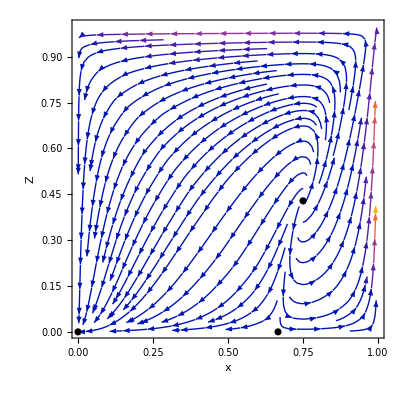

```mathematica
Show[PhaseSpaceCompactxz,FPShowCompactxz]
```

### Compact x - y - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(1. X (2.+1. X))/(4.-6. X+5. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→-2.,Y→0.,Z→0.},{X→0.,Y→0.,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.745356,Z→0.428571},{X→0.75,Y→0.745356,Z→0.428571},{X→0.75,Y→0.,Z→0.891892}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]]};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z)))/((-1.+X) √(1-Y^2) (-1.+Z)) | (X (-1.5+X (2.25-1.25 Z)+0.5 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.166667 (0.5+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.-2.5 Z+Y^2 (-3.+3.5 Z)+X (-3.75+Y^2 (5.75-6.75 Z)+4.75 Z)+X^2 (2.125-2.625 Z+Y^2 (-3.125+3.625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(1. X (2.+1. X))/(4.-6. X+5. X^2)) | (0. | (2.5 X (-0.6+1.9 X-2.3 X^2+1. X^3))/(1.-1. X)^2 | 0.
(-0.0833333-0.166667 X)/(-1.+X)^3 | 0. | -(0.260417 (0.8-1.2 X+1. X^2)^2)/(1.-1. X)^4
0. | (X (0.96-2.72 X+1.92 X^2+0.48 X^3-0.64 X^4))/((-1.+X) (0.8-1.2 X+1. X^2)^2) | 0.) | (0
-((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)
((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)) | (-(1.5625 (-1.+X)^3 (0.8-1.2 X+1. X^2)^2)/((0.5+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (0.48-6.8 X+45.2 X^2-183.88 X^3+494.17 X^4-843.615 X^5+568.515 X^6+1551.82 X^7-6511.75 X^8+13756.4 X^9-20660.5 X^10+23903.7 X^11-21903.5 X^12+16008.1 X^13-9277.91 X^14+4189.86 X^15-1426.58 X^16+345.43 X^17-53.125 X^18+3.90625 X^19))/((-1.+1. X)^6 (-0.75+1. X) (0.5+1. X) (2.+1. X) (1.-2. X+1. X^2)^2 (0.8-1.2 X+1. X^2)^2) | ((0.+6.58545×10^-8 ⅈ) √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+X)^3 √X (-1.+1. X) (2.+1. X) (-3.+4. X) (1.-2. X+1. X^2)) | 1.
-(1. (0.48-6.8 X+45.2 X^2-183.88 X^3+494.17 X^4-843.615 X^5+568.515 X^6+1551.82 X^7-6511.75 X^8+13756.4 X^9-20660.5 X^10+23903.7 X^11-21903.5 X^12+16008.1 X^13-9277.91 X^14+4189.86 X^15-1426.58 X^16+345.43 X^17-53.125 X^18+3.90625 X^19))/((-1.+1. X)^6 (-0.75+1. X) (0.5+1. X) (2.+1. X) (1.-2. X+1. X^2)^2 (0.8-1.2 X+1. X^2)^2) | -((0.+6.58545×10^-8 ⅈ) √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+X)^3 √X (-1.+1. X) (2.+1. X) (-3.+4. X) (1.-2. X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.22474 | 0. | 0.181444
2.43998 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0872861 | -0.167684 | 0.981969)
(-2.
0.
0.) | (0. | 12. | 0.
-0.00925926 | 0. | -0.166667
0. | 0. | 0.) | (0.+0.333333 ⅈ
0.-0.333333 ⅈ
0.+0. ⅈ) | (0.999614+0. ⅈ | 0.+0.0277671 ⅈ | 0.+0. ⅈ
0.999614+0. ⅈ | 0.-0.0277671 ⅈ | 0.+0. ⅈ
-0.99846+0. ⅈ | 0.+0. ⅈ | 0.05547+0. ⅈ)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -0.166667
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(0.666667
0.632456
0.) | (1.22474 | 0. | -0.181444
2.43998 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0872861 | 0.167684 | 0.981969)
(0.75
-0.745356
0.428571) | (-2.51558 | 3.68846×10^-16 | 0.641996
3.95062 | 2.23607 | -0.151235
-4.38087 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (3.23995×10^-17+0. ⅈ | 1.+0. ⅈ | -5.87032×10^-17+0. ⅈ
0.2525-0.222684 ⅈ | -0.297406+0.157372 ⅈ | 0.879454+0. ⅈ
0.2525+0.222684 ⅈ | -0.297406-0.157372 ⅈ | 0.879454+0. ⅈ)
(0.75
0.745356
0.428571) | (2.51558 | 3.68846×10^-16 | -0.641996
3.95062 | -2.23607 | -0.151235
4.38087 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (3.23995×10^-17+0. ⅈ | -1.+0. ⅈ | -5.87032×10^-17+0. ⅈ
0.2525+0.222684 ⅈ | 0.297406+0.157372 ⅈ | 0.879454+0. ⅈ
0.2525-0.222684 ⅈ | 0.297406-0.157372 ⅈ | 0.879454+0. ⅈ)
(0.75
0.
0.891892) | (0. | -1.40625 | 0.
13.3333 | 0. | -14.2604
0. | 0. | 0.) | (0.+4.33013 ⅈ
0.-4.33013 ⅈ
0.+0. ⅈ) | (0.-0.308879 ⅈ | -0.951101+0. ⅈ | 0.+0. ⅈ
0.+0.308879 ⅈ | -0.951101+0. ⅈ | 0.+0. ⅈ
0.730452+0. ⅈ | 0.+0. ⅈ | 0.682964+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPShow=ListPointPlot3D[Table[FP[i],{i,2,8}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFPs=ParametricPlot3D[{X,0,(X *(2+ X))/(4-6* X+5* X^2)},{X,0,1},{Z,0,1},PlotStyle->{{Thickness[0.01],Red}}];
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->Darker[Green]];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->Darker[Green]];
```

```mathematica
EqX[q_,wx_,ϵ_]=deX;
EqY[wx_,ϵ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
PhaseSpace3D=StreamPlot3D[{EqX[q,wx,ϵ],EqY[wx,ϵ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamPoints->20(*RandomReal[{-1,1},{20,3}]*),StreamScale->{Full},StreamMarkers->"Arrow",StreamColorFunction->None];
```

Min::nord: Invalid comparison with -1.46372+1.0678×10^-7 ⅈ attempted.

Max::nord: Invalid comparison with -1.46372+1.0678×10^-7 ⅈ attempted.

```mathematica
Show[PhaseSpace3D,EinsteinFPs,FPShow,CompactFPShow,FFSPlus,FFSMinus]
```

-Graphics3D-

## Numeric Compact Phase Spaces

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
deA:=A'=A*(1-A)*Y/((1-Y)^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0,deA==0},{X,Y,Z,A}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(1. X (2.+1. X))/(4.-6. X+5. X^2)},{X→-2.,Y→0.,Z→0.},{X→0.,Y→0.,Z→0.},{X→0.75,Y→0.,Z→0.891892},{X→0.666667,Y→-0.632456,Z→0.,A→0.},{X→0.666667,Y→0.632456,Z→0.,A→0.},{X→0.75,Y→-0.745356,Z→0.428571,A→0.},{X→0.75,Y→0.745356,Z→0.428571,A→0.},{X→0.666667,Y→-0.632456,Z→0.,A→1.},{X→0.666667,Y→0.632456,Z→0.,A→1.},{X→0.75,Y→-0.745356,Z→0.428571,A→1.},{X→0.75,Y→0.745356,Z→0.428571,A→1.}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]],A};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]],A};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]],A};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]],A};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]],A/.FPs[[5,4]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]],A/.FPs[[6,4]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]],A/.FPs[[7,4]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]],A/.FPs[[8,4]]};
FP[9]={X/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]],A/.FPs[[9,4]]};
FP[10]={X/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]],A/.FPs[[10,4]]};
FP[11]={X/.FPs[[11,1]],Y/.FPs[[11,2]],Z/.FPs[[11,3]],A/.FPs[[11,4]]};
FP[12]={X/.FPs[[12,1]],Y/.FPs[[12,2]],Z/.FPs[[12,3]],A/.FPs[[12,4]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,12}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z],D[deX,A]},{D[deY,X],D[deY,Y],D[deY,Z],D[deY,A]},{D[deZ,X],D[deZ,Y],D[deZ,Z],D[deZ,A]},{D[deA,X],D[deA,Y],D[deA,Z],D[deA,A]}}];
J//MatrixForm
```

((Y (-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z)))/((-1.+X) √(1-Y^2) (-1.+Z)) | (X (-1.5+X (2.25-1.25 Z)+0.5 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2) | 0
(0.166667 (0.5+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.-2.5 Z+Y^2 (-3.+3.5 Z)+X (-3.75+Y^2 (5.75-6.75 Z)+4.75 Z)+X^2 (2.125-2.625 Z+Y^2 (-3.125+3.625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | 0
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)) | 0
0 | ((-1+A) A (-2+Y))/(2 (1-Y)^(3/2)) | 0 | (Y-2 A Y)/(√(1-Y)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],A->FPs[[i,4]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],A->FPs[[i,4]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],A->FPs[[i,4]]}]//MatrixForm},{i,1,12}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(1. X (2.+1. X))/(4.-6. X+5. X^2)
A) | (0. | (2.5 X (-0.6+1.9 X-2.3 X^2+1. X^3))/(1.-1. X)^2 | 0. | 0
(-0.0833333-0.166667 X)/(-1.+X)^3 | 0. | -(0.260417 (0.8-1.2 X+1. X^2)^2)/(1.-1. X)^4 | 0
0. | (X (0.96-2.72 X+1.92 X^2+0.48 X^3-0.64 X^4))/((-1.+X) (0.8-1.2 X+1. X^2)^2) | 0. | 0
0 | -1. (-1.+A) A | 0 | 0.) | (0
0
-((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)
((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)) | (0 | 0 | 0 | 1.
-(1.5625 (-1.+X)^3 (0.8-1.2 X+1. X^2)^2)/((0.5+1. X) (1.-2. X+1. X^2)^2) | 0 | 1. | 0
-(2.5 X (-0.6+1.9 X-2.3 X^2+1. X^3))/((-1.+A) A (1.-2. X+1. X^2)) | ((0.+1.05367×10^-8 ⅈ) √X √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+A) A (-1.+X)^4 (-1.+1. X) (0.8-1.2 X+1. X^2)^2) | (0.64 X (-0.75+1. X) (2.+1. X) (1.-2. X+1. X^2))/((-1.+A) A (-1.+X) (0.8-1.2 X+1. X^2)^2) | 1.
-(2.5 X (-0.6+1.9 X-2.3 X^2+1. X^3))/((-1.+A) A (1.-2. X+1. X^2)) | -((0.+1.05367×10^-8 ⅈ) √X √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+A) A (-1.+X)^4 (-1.+1. X) (0.8-1.2 X+1. X^2)^2) | (0.64 X (-0.75+1. X) (2.+1. X) (1.-2. X+1. X^2))/((-1.+A) A (-1.+X) (0.8-1.2 X+1. X^2)^2) | 1.)
(-2.
0.
0.
A) | (0. | 12. | 0. | 0
-0.00925926 | 0. | -0.166667 | 0
0. | 0. | 0. | 0
0 | -1. (-1.+A) A | 0 | 0.) | (0.+0.333333 ⅈ
0.-0.333333 ⅈ
0
0) | (-12./((-1.+A) A) | -(0.+0.333333 ⅈ)/((-1.+A) A) | 0 | 1.
-12./((-1.+A) A) | (0.+0.333333 ⅈ)/((-1.+A) A) | 0 | 1.
0 | 0 | 0 | 1.
-18. | 0 | 1. | 0)
(0.
0.
0.
A) | (0. | 0. | 0. | 0
0.0833333 | 0. | -0.166667 | 0
0. | 0. | 0. | 0
0 | -1. (-1.+A) A | 0 | 0.) | (0
0
0
0) | (0. | 0. | 0. | 1.
2. | 0. | 1. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0.75
0.
0.891892
A) | (0. | -1.40625 | 0. | 0
13.3333 | 0. | -14.2604 | 0
0. | 0. | 0. | 0
0 | -1. (-1.+A) A | 0 | 0.) | (0.+4.33013 ⅈ
0.-4.33013 ⅈ
0
0) | (1.40625/((-1.+A) A) | -(0.+4.33013 ⅈ)/((-1.+A) A) | 0 | 1.
1.40625/((-1.+A) A) | (0.+4.33013 ⅈ)/((-1.+A) A) | 0 | 1.
0 | 0 | 0 | 1.
1.06953 | 0 | 1. | 0)
(0.666667
-0.632456
0.
0.) | (-1.22474 | 0. | 0.181444 | 0
2.43998 | 1.63299 | -0.0774597 | 0
0. | 0. | 0.816497 | 0
0 | 0. | 0 | -0.495005) | (1.63299
-1.22474
0.816497
-0.495005) | (0. | 1. | 0. | 0.
0.760506 | -0.649331 | 0. | 0.
0.0872861 | -0.167684 | 0.981969 | 0.
0. | 0. | 0. | 1.)
(0.666667
0.632456
0.
0.) | (1.22474 | 0. | -0.181444 | 0
2.43998 | -1.63299 | -0.0774597 | 0
0. | 0. | -0.816497 | 0
0 | 0. | 0 | 1.04322) | (-1.63299
1.22474
1.04322
-0.816497) | (0. | 1. | 0. | 0.
0.760506 | 0.649331 | 0. | 0.
0. | 0. | 0. | 1.
0.0872861 | 0.167684 | 0.981969 | 0.)
(0.75
-0.745356
0.428571
0.) | (-2.51558 | 3.68846×10^-16 | 0.641996 | 0
3.95062 | 2.23607 | -0.151235 | 0
-4.38087 | 0. | 0. | 0
0 | 0. | 0 | -0.564185) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ
-0.564185+0. ⅈ) | (3.23995×10^-17+0. ⅈ | 1.+0. ⅈ | -5.87032×10^-17+0. ⅈ | 0.+0. ⅈ
0.2525-0.222684 ⅈ | -0.297406+0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.2525+0.222684 ⅈ | -0.297406-0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)
(0.75
0.745356
0.428571
0.) | (2.51558 | 3.68846×10^-16 | -0.641996 | 0
3.95062 | -2.23607 | -0.151235 | 0
4.38087 | 0. | 0. | 0
0 | 0. | 0 | 1.47706) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ
1.47706+0. ⅈ) | (3.23995×10^-17+0. ⅈ | -1.+0. ⅈ | -5.87032×10^-17+0. ⅈ | 0.+0. ⅈ
0.2525+0.222684 ⅈ | 0.297406+0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.2525-0.222684 ⅈ | 0.297406-0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)
(0.666667
-0.632456
0.
1.) | (-1.22474 | 0. | 0.181444 | 0
2.43998 | 1.63299 | -0.0774597 | 0
0. | 0. | 0.816497 | 0
0 | 0. | 0 | 0.495005) | (1.63299
-1.22474
0.816497
0.495005) | (0. | 1. | 0. | 0.
0.760506 | -0.649331 | 0. | 0.
0.0872861 | -0.167684 | 0.981969 | 0.
0. | 0. | 0. | 1.)
(0.666667
0.632456
0.
1.) | (1.22474 | 0. | -0.181444 | 0
2.43998 | -1.63299 | -0.0774597 | 0
0. | 0. | -0.816497 | 0
0 | 0. | 0 | -1.04322) | (-1.63299
1.22474
-1.04322
-0.816497) | (0. | 1. | 0. | 0.
0.760506 | 0.649331 | 0. | 0.
0. | 0. | 0. | 1.
0.0872861 | 0.167684 | 0.981969 | 0.)
(0.75
-0.745356
0.428571
1.) | (-2.51558 | 3.68846×10^-16 | 0.641996 | 0
3.95062 | 2.23607 | -0.151235 | 0
-4.38087 | 0. | 0. | 0
0 | 0. | 0 | 0.564185) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ
0.564185+0. ⅈ) | (3.23995×10^-17+0. ⅈ | 1.+0. ⅈ | -5.87032×10^-17+0. ⅈ | 0.+0. ⅈ
0.2525-0.222684 ⅈ | -0.297406+0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.2525+0.222684 ⅈ | -0.297406-0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)
(0.75
0.745356
0.428571
1.) | (2.51558 | 3.68846×10^-16 | -0.641996 | 0
3.95062 | -2.23607 | -0.151235 | 0
4.38087 | 0. | 0. | 0
0 | 0. | 0 | -1.47706) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ
-1.47706+0. ⅈ) | (3.23995×10^-17+0. ⅈ | -1.+0. ⅈ | -5.87032×10^-17+0. ⅈ | 0.+0. ⅈ
0.2525+0.222684 ⅈ | 0.297406+0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.2525-0.222684 ⅈ | 0.297406-0.157372 ⅈ | 0.879454+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)

### X-Y-Z Phase Space

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
deA:=A'=A*(1-A)*Y/((1-Y^2)^(1/2))
```

```mathematica
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(1. X (2.+1. X))/(4.-6. X+5. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→-2.,Y→0.,Z→0.},{X→0.,Y→0.,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.745356,Z→0.428571},{X→0.75,Y→0.745356,Z→0.428571},{X→0.75,Y→0.,Z→0.891892}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]]};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
FPsXYZ=ListPointPlot3D[FPs,PlotStyle->Black];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z)))/((-1.+X) √(1-Y^2) (-1.+Z)) | (X (-1.5+X (2.25-1.25 Z)+0.5 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.166667 (0.5+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.-2.5 Z+Y^2 (-3.+3.5 Z)+X (-3.75+Y^2 (5.75-6.75 Z)+4.75 Z)+X^2 (2.125-2.625 Z+Y^2 (-3.125+3.625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(1. X (2.+1. X))/(4.-6. X+5. X^2)) | (0. | (2.5 X (-0.6+1.9 X-2.3 X^2+1. X^3))/(1.-1. X)^2 | 0.
(-0.0833333-0.166667 X)/(-1.+X)^3 | 0. | -(0.260417 (0.8-1.2 X+1. X^2)^2)/(1.-1. X)^4
0. | (X (0.96-2.72 X+1.92 X^2+0.48 X^3-0.64 X^4))/((-1.+X) (0.8-1.2 X+1. X^2)^2) | 0.) | (0
-((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)
((0.+6.58545×10^-8 ⅈ) √X √(-7.3787×10^15+1.1437×10^17 X-8.44861×10^17 X^2+3.97158×10^18 X^3-1.33458×10^19 X^4+3.40787×10^19 X^5-6.85534×10^19 X^6+1.1106×10^20 X^7-1.46805×10^20 X^8+1.59355×10^20 X^9-1.42158×10^20 X^10+1.03716×10^20 X^11-6.11856×10^19 X^12+2.86035×10^19 X^13-1.02441×10^19 X^14+2.65136×10^18 X^15-4.43154×10^17 X^16+3.60288×10^16 X^17))/((-1.+X)^4 (-1.+1. X) (4.-6. X+5. X^2)^2)) | (-(1.5625 (-1.+X)^3 (0.8-1.2 X+1. X^2)^2)/((0.5+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (0.48-6.8 X+45.2 X^2-183.88 X^3+494.17 X^4-843.615 X^5+568.515 X^6+1551.82 X^7-6511.75 X^8+13756.4 X^9-20660.5 X^10+23903.7 X^11-21903.5 X^12+16008.1 X^13-9277.91 X^14+4189.86 X^15-1426.58 X^16+345.43 X^17-53.125 X^18+3.90625 X^19))/((-1.+1. X)^6 (-0.75+1. X) (0.5+1. X) (2.+1. X) (1.-2. X+1. X^2)^2 (0.8-1.2 X+1. X^2)^2) | ((0.+6.58545×10^-8 ⅈ) √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+X)^3 √X (-1.+1. X) (2.+1. X) (-3.+4. X) (1.-2. X+1. X^2)) | 1.
-(1. (0.48-6.8 X+45.2 X^2-183.88 X^3+494.17 X^4-843.615 X^5+568.515 X^6+1551.82 X^7-6511.75 X^8+13756.4 X^9-20660.5 X^10+23903.7 X^11-21903.5 X^12+16008.1 X^13-9277.91 X^14+4189.86 X^15-1426.58 X^16+345.43 X^17-53.125 X^18+3.90625 X^19))/((-1.+1. X)^6 (-0.75+1. X) (0.5+1. X) (2.+1. X) (1.-2. X+1. X^2)^2 (0.8-1.2 X+1. X^2)^2) | -((0.+6.58545×10^-8 ⅈ) √(-4.61169×10^14+7.14811×10^15 X-5.28038×10^16 X^2+2.48224×10^17 X^3-8.3411×10^17 X^4+2.12992×10^18 X^5-4.28459×10^18 X^6+6.94124×10^18 X^7-9.17529×10^18 X^8+9.9597×10^18 X^9-8.88485×10^18 X^10+6.48224×10^18 X^11-3.8241×10^18 X^12+1.78772×10^18 X^13-6.40259×10^17 X^14+1.6571×10^17 X^15-2.76971×10^16 X^16+2.2518×10^15 X^17))/((-1.+X)^3 √X (-1.+1. X) (2.+1. X) (-3.+4. X) (1.-2. X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.22474 | 0. | 0.181444
2.43998 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0872861 | -0.167684 | 0.981969)
(-2.
0.
0.) | (0. | 12. | 0.
-0.00925926 | 0. | -0.166667
0. | 0. | 0.) | (0.+0.333333 ⅈ
0.-0.333333 ⅈ
0.+0. ⅈ) | (0.999614+0. ⅈ | 0.+0.0277671 ⅈ | 0.+0. ⅈ
0.999614+0. ⅈ | 0.-0.0277671 ⅈ | 0.+0. ⅈ
-0.99846+0. ⅈ | 0.+0. ⅈ | 0.05547+0. ⅈ)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -0.166667
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(0.666667
0.632456
0.) | (1.22474 | 0. | -0.181444
2.43998 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0872861 | 0.167684 | 0.981969)
(0.75
-0.745356
0.428571) | (-2.51558 | 3.68846×10^-16 | 0.641996
3.95062 | 2.23607 | -0.151235
-4.38087 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (3.23995×10^-17+0. ⅈ | 1.+0. ⅈ | -5.87032×10^-17+0. ⅈ
0.2525-0.222684 ⅈ | -0.297406+0.157372 ⅈ | 0.879454+0. ⅈ
0.2525+0.222684 ⅈ | -0.297406-0.157372 ⅈ | 0.879454+0. ⅈ)
(0.75
0.745356
0.428571) | (2.51558 | 3.68846×10^-16 | -0.641996
3.95062 | -2.23607 | -0.151235
4.38087 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (3.23995×10^-17+0. ⅈ | -1.+0. ⅈ | -5.87032×10^-17+0. ⅈ
0.2525+0.222684 ⅈ | 0.297406+0.157372 ⅈ | 0.879454+0. ⅈ
0.2525-0.222684 ⅈ | 0.297406-0.157372 ⅈ | 0.879454+0. ⅈ)
(0.75
0.
0.891892) | (0. | -1.40625 | 0.
13.3333 | 0. | -14.2604
0. | 0. | 0.) | (0.+4.33013 ⅈ
0.-4.33013 ⅈ
0.+0. ⅈ) | (0.-0.308879 ⅈ | -0.951101+0. ⅈ | 0.+0. ⅈ
0.+0.308879 ⅈ | -0.951101+0. ⅈ | 0.+0. ⅈ
0.730452+0. ⅈ | 0.+0. ⅈ | 0.682964+0. ⅈ)

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deAt:=A1'[t]==A1[t]*(1-A1[t])*Y1[t]/((1-Y1[t]^2)^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Plot the FFS*)
ffs=(1/3)*(X/(1-X)+Z/(1-Z));
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
FFSPlus=ParametricPlot3D[{X,FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
FFSMinus=ParametricPlot3D[{X,-FFS,Z},{X,0,1},{Z,0,1},PlotStyle->{{Darker[Green],Opacity[0.25]}},Mesh->None];
```

```mathematica
traj[X0_,Y0_,Z0_]=NDSolve[{deXt,deYt,deZt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0}, {X1,Y1,Z1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition X0 is not a number or a rectangular array of numbers.

```mathematica
(*Define initial conditions for the flat cases*)
FlatX0=0.7;
FlatZ0=0.7;
FlatY0=Sqrt[(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0))))/(1+(FlatX0/(3*(1-FlatX0))+(FlatZ0/(3*(1-FlatZ0)))))];
```

```mathematica
FlatX0i=0.1;
FlatZ0i=0.1;
FlatY0i=Sqrt[(FlatX0i/(3*(1-FlatX0i))+(FlatZ0i/(3*(1-FlatZ0i))))/(1+(FlatX0i/(3*(1-FlatX0i))+(FlatZ0i/(3*(1-FlatZ0i)))))];
```

```mathematica
FlatX0ii=0.7;
FlatZ0ii=0.1;
FlatY0ii=Sqrt[(FlatX0ii/(3*(1-FlatX0ii))+(FlatZ0ii/(3*(1-FlatZ0ii))))/(1+(FlatX0ii/(3*(1-FlatX0ii))+(FlatZ0ii/(3*(1-FlatZ0ii)))))];
```

```mathematica
FlatX0iii=0.751;
FlatZ0iii=0.42857142857142855;
FlatY0iii=Sqrt[(FlatX0iii/(3*(1-FlatX0iii))+(FlatZ0iii/(3*(1-FlatZ0iii))))/(1+(FlatX0iii/(3*(1-FlatX0iii))+(FlatZ0iii/(3*(1-FlatZ0iii)))))];
```

```mathematica
FlatX0iv=0.5;
FlatZ0iv=0.5;
FlatY0iv=Sqrt[(FlatX0iv/(3*(1-FlatX0iv))+(FlatZ0iv/(3*(1-FlatZ0iv))))/(1+(FlatX0iv/(3*(1-FlatX0iv))+(FlatZ0iv/(3*(1-FlatZ0iv)))))];
```

```mathematica
(*Flat trajectories*)
sol[1]=traj[FlatX0,FlatY0,FlatZ0]
sol[2]=traj[FlatX0,-FlatY0,FlatZ0]
```

{{(X1→InterpolatingFunction[…]) (X1→InterpolatingFunction[…]),(Y1→InterpolatingFunction[…]) (Y1→InterpolatingFunction[…]),(Z1→InterpolatingFunction[…]) (Z1→InterpolatingFunction[…])}}

```mathematica
sol[3]=traj[FlatX0i,FlatY0i,FlatZ0i]
sol[4]=traj[FlatX0i,-FlatY0i,FlatZ0i]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
sol[5]=traj[FlatX0ii,FlatY0ii,FlatZ0ii]
sol[6]=traj[FlatX0ii,-FlatY0ii,FlatZ0ii]
```

NDSolve::mxst: Maximum number of 311552 steps reached at the point t == -10.3679.

{{X1→InterpolatingFunction[{{-10.3679, 100.}}, <>],Y1→InterpolatingFunction[{{-10.3679, 100.}}, <>],Z1→InterpolatingFunction[{{-10.3679, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 311552 steps reached at the point t == 10.375.

{{X1→InterpolatingFunction[{{-100., 10.375}}, <>],Y1→InterpolatingFunction[{{-100., 10.375}}, <>],Z1→InterpolatingFunction[{{-100., 10.375}}, <>]}}

```mathematica
sol[7]=traj[FlatX0iii,FlatY0iii,FlatZ0iii]
sol[8]=traj[FlatX0iii,-FlatY0iii,FlatZ0iii]
```

NDSolve::mxst: Maximum number of 99581 steps reached at the point t == -10.9595.

{{X1→InterpolatingFunction[{{-10.9595, 100.}}, <>],Y1→InterpolatingFunction[{{-10.9595, 100.}}, <>],Z1→InterpolatingFunction[{{-10.9595, 100.}}, <>]}}

NDSolve::mxst: Maximum number of 99581 steps reached at the point t == 10.9595.

{{X1→InterpolatingFunction[{{-100., 10.9595}}, <>],Y1→InterpolatingFunction[{{-100., 10.9595}}, <>],Z1→InterpolatingFunction[{{-100., 10.9595}}, <>]}}

```mathematica
sol[9]=traj[FlatX0iv,FlatY0iv,FlatZ0iv]
sol[10]=traj[FlatX0iv,-FlatY0iv,FlatZ0iv]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Closed trajectories*)
sol[11]=traj[0.3,0.1,0.3]
sol[12]=traj[0.9,0,0.6]
sol[13]=traj[0.9,0,0.8]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
(*Open trajectories*)
sol[14]=traj[0.1,-0.75,0.1] 
sol[15]=traj[0.1,0.75,0.1]
```

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {0.880689,0.75+0. ⅈ,-1.+0. ⅈ,0.428571+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::ndcf: Repeated convergence test failure at t == -0.880689; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
PhaseSpacexy1=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[1],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy2=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[2],{t,-100,100},PlotStyle -> {{Darker[Green], Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy3=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[3], {t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy4=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[4],{t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy5=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[5],{t,-10.3,100},PlotStyle -> {{Purple, Opacity[0.75]}}],AxesLabel->{"X","Y","Z"},PlotPoints->500];
```

```mathematica
PhaseSpacexy6=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[6],{t,-100,10.3},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy7=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[7],{t,-10.9,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy8=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[8],{t,-100,10.9},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy9=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[9],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy10=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[10],{t,-100,100},PlotStyle -> {{Brown, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy11=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[11],{t,-100,100},PlotStyle -> {{Orange, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy12=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[12],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy13=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[13],{t,-100,100},PlotStyle -> {{Magenta, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy14=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[14],{t,-100,0.88},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
PhaseSpacexy15=ParametricPlot3D[Evaluate[{X1[t],Y1[t],Z1[t]}/.sol[15],{t,-0.88,100},PlotStyle -> {{Pink, Opacity[0.75]}}],PlotPoints->500,AxesLabel->{"X","Y","Z"}];
```

```mathematica
Show[PhaseSpacexy11,PhaseSpacexy12,PhaseSpacexy13,PhaseSpacexy14,PhaseSpacexy15,FPsXYZ,FFSPlus,FFSMinus,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
Show[PhaseSpacexy3,PhaseSpacexy4,PhaseSpacexy5,PhaseSpacexy6,(*PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy7,PhaseSpacexy8,PhaseSpacexy9,PhaseSpacexy10,*)FFSPlus,FFSMinus,FPsXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
Show[PhaseSpacexy7,PhaseSpacexy8,(*PhaseSpacexy1,PhaseSpacexy2,PhaseSpacexy7,PhaseSpacexy8,PhaseSpacexy9,PhaseSpacexy10,*)FFSPlus,FFSMinus,FPsXYZ,PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

### Z = 0.009

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deAt:=A1'[t]==A1[t]*(1-A1[t])*Y1[t]/((1-Y1[t])^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Plot the fixed points*)
FPShowNumericxy=ListPlot[{{-2,0},{0,0},{0.75,0}(*,{0.6666666666666666,-0.6324555320336759},{0.6666666666666666,0.6324555320336759},{0.75,-0.7453559924999299},{0.75,0.7453559924999299}*)},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
traj[X0_,Y0_,Z0_,A0_]=NDSolve[{deXt,deYt,deZt,deAt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0,A1[0]==A0}, {X1,Y1,Z1,A1},{t,-80,80},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->10000];
```

NDSolve::ndinnt: Initial condition A0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.009,1/2];
sol[2]=traj[0.8,0.75,0.009,1/2];
sol[3]=traj[0.6,0.65,0.009,1/2];
sol[4]=traj[0.5,0.1,0.009,1/2];
sol[5]=traj[0.5,0.3,0.009,1/2];
sol[6]=traj[0.5,0.741,0.009,1/2]; 
sol[7]=traj[0.5,0.8,0.009,1/2];
sol[8]=traj[0.1,0.5,0.009,1/2];
sol[9]=traj[0.02,0.5,0.009,1/2];
sol[10]=traj[0.02,0.8,0.009,1/2];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.63711.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.15742.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -0.811994.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.7689.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.79255.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -0.951791.

```mathematica
sol[11]=traj[0.1,-0.1,0.009,1/2];
sol[12]=traj[0.8,-0.75,0.009,1/2];
sol[13]=traj[0.6,-0.65,0.009,1/2];
sol[14]=traj[0.5,-0.1,0.009,1/2];
sol[15]=traj[0.5,-0.3,0.009,1/2];
sol[16]=traj[0.5,-0.741,0.009,1/2]; 
sol[17]=traj[0.5,-0.8,0.009,1/2];
sol[18]=traj[0.1,-0.5,0.009,1/2];
sol[19]=traj[0.02,-0.5,0.009,1/2];
sol[20]=traj[0.02,-0.8,0.009,1/2];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.99879.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.01657.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.82101.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.87232.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.82648.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.749661.

```mathematica
sol[21]=traj[0.5,0.741,0.009,1/2]; 
sol[22]=traj[0.5,-0.741,0.009,1/2];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.15742.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.01657.

```mathematica
PhaseSpacexy=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,20}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
PhaseSpaceFFS=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,21,22}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

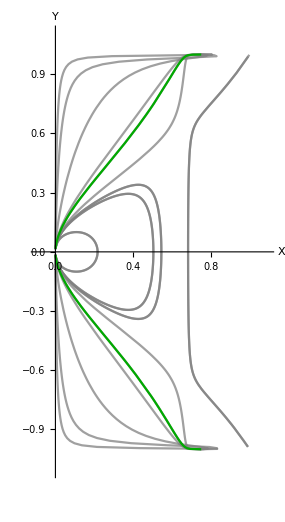

```mathematica
Show[PhaseSpacexy,PhaseSpaceFFS]
```

```mathematica
(*FPShowNumericay=ListPlot[{{0.,-0.6324555320336759},{0.,0.6324555320336759},{0.,-0.7453559924999299},{0.,0.7453559924999299},{1.,-0.6324555320336759},{1.,0.6324555320336759},{1.,-0.7453559924999299},{1.,0.7453559924999299}},PlotStyle->Black];*)
```

```mathematica
(*Plot A-Y phase space*)
PhaseSpaceNumericay=ParametricPlot[Evaluate[Table[{A1[t],Y1[t]}/.sol[i],{i,1,20}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"A","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

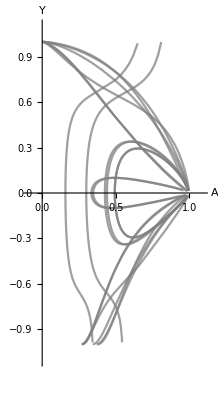

```mathematica
Show[PhaseSpaceNumericay]
```

### Z = 0.9

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deAt:=A1'[t]==A1[t]*(1-A1[t])*Y1[t]/((1-Y1[t])^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
traj[X0_,Y0_,Z0_,A0_]=NDSolve[{deXt,deYt,deZt,deAt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0,A1[0]==A0}, {X1,Y1,Z1,A1},{t,-80,80},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->10000];
```

NDSolve::ndinnt: Initial condition A0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.9,1/2];
sol[2]=traj[0.8,0.75,0.9,1/2];
sol[3]=traj[0.6,0.65,0.9,1/2];
sol[4]=traj[0.5,0.1,0.9,1/2];
sol[5]=traj[0.5,0.3,0.9,1/2];
sol[6]=traj[0.5,0.741,0.9,1/2]; 
sol[7]=traj[0.5,0.8,0.9,1/2];
sol[8]=traj[0.1,0.5,0.9,1/2];
sol[9]=traj[0.02,0.5,0.9,1/2];
sol[10]=traj[0.02,0.8,0.9,1/2];
```

```mathematica
sol[11]=traj[0.02,0.554,0.9,1/2]; 
sol[12]=traj[0.02,-0.554,0.9,1/2];
```

```mathematica
FPShowNumericxy=ListPlot[{{0.75,0}},PlotStyle->{Black,PointSize[.02]}];
```

```mathematica
PhaseSpaceXY=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,10}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

```mathematica
PhaseSpaceFFS2=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,11,12}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

Show::gcomb: Could not combine the graphics objects in Show[,].

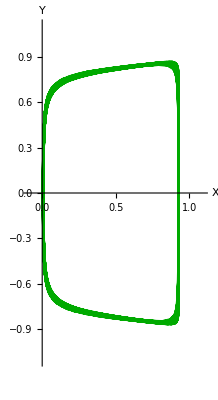
Show[-Graphics3D-,-Graphics-]

```mathematica
Show[PhaseSpacexy2,PhaseSpaceFFS2]
```

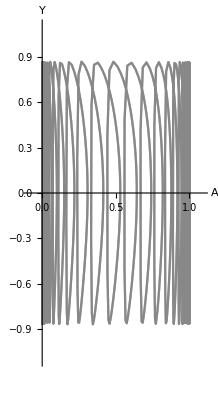

```mathematica
PhaseSpaceXY2=ParametricPlot[Evaluate[Table[{A1[t],Y1[t]}/.sol[12],{i,1,2}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"A","Y"}]
```